## Numerical plot for α,β

```mathematica
α=3;
β=2;
i[n_?NumericQ,τ_?NumericQ]:=NIntegrate[x^(β-1)/(1+x)^(α+β)E^(-2(n+1)^2(1+x)^2/τ),{x,0,∞},Method->"GlobalAdaptive"];
g[τ_?NumericQ]:=(2(α-1))/((α+1)Beta[α,β])NSum[Pochhammer[(3-α)/2,n]/Pochhammer[(3+α)/2,n] i[n,τ],{n,0,IntegerPart[√τ]},Method->"WynnEpsilon"];
```

```mathematica
τ=1000.
β √(2/(π τ))(1-g[τ])
Clear[τ]
```

1000.

0.00185399

```mathematica
tableg=Table[{τ,β √(2/(π τ))(1-g[τ])}/.τ->10^k,{k,-4.,5.,0.05}];
tablegth=Table[{τ,gth[τ]}/.τ->10^k,{k,-4.,5.,0.05}];
tabletauexp=Table[tableg[[i]][[1]],{i,1,Length[tableg]}];
tablegexp=Table[tableg[[i]][[2]],{i,1,Length[tableg]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
Export["C:\\Travail\\Mathematica\\SATW\\Records\\s-phi-nonzerosat-alpha3-beta1over6.csv",tablegexp]
Export["C:\\Travail\\Mathematica\\SATW\\Records\\tau-phi-nonzerosat-alpha3-beta1over6.csv",tabletauexp]
```

C:\Travail\Mathematica\SATW\Records\s-phi-nonzerosat-alpha3-beta1over6.csv

C:\Travail\Mathematica\SATW\Records\tau-phi-nonzerosat-alpha3-beta1over6.csv

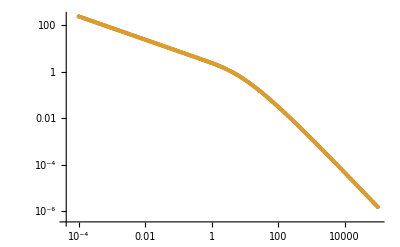

```mathematica
ListLogLogPlot[{tableg,tablegth},PlotRange->All]
```

## Nonzero saturation

```mathematica
weightsat[n_,ϕ_]:=1/ϕ+(1-1/ϕ)(2/(1+E^-n)-1);
ϕ=3;
weightsat[0,ϕ]^-1+NSum[weightsat[2j,ϕ]^-1-weightsat[2j-1,ϕ]^-1,{j,1,∞}]
```

2.58039

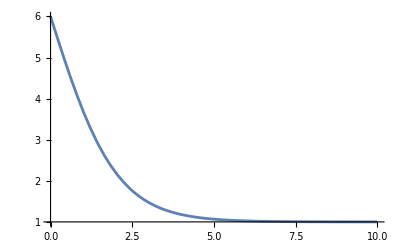

```mathematica
Plot[weightsat[n,1/6],{n,0,10},PlotRange->All]
```

## Numerical tests of integral equalities

```mathematica
ϕ=3/4;
μ=0.000000000001;
k=1;
(*NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)Coth[(1+m)μ],{m,0,∞}];
(*μ ϕ NIntegrate[m1^(ϕ-1)/(1+m1)^(2ϕ)Sinh[μ(1+m1)]^(ϕ-1)/Sinh[μ(1+m2)]^(ϕ+1),{m1,0,∞},{m2,m1,∞},Method->"LocalAdaptive"]*)
2 ϕ/(1+ϕ) NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)(Coth[(1+m)μ]-1)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)],{m,0,∞},Method->"GlobalAdaptive"];
%/%%;*)
μ/Beta[ϕ,ϕ] NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)Coth[(1+m)μ]-2 ϕ/(1+ϕ)m^(ϕ-1)/(1+m)^(2ϕ)(Coth[(1+m)μ]-1)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)],{m,0,∞}]

μ/Beta[ϕ,ϕ] NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)(Coth[(1+m)μ](1-2 ϕ/(1+ϕ)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)])+2 ϕ/(1+ϕ)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)]),{m,0,∞},Method->"GlobalAdaptive"]
μ(1-1/Beta[ϕ,ϕ] NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)E^(-μ(1+m))/Sinh[μ(1+m)](2 ϕ/(1+ϕ)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)]-1),{m,0,∞},Method->"GlobalAdaptive"])
μ(1-(2(ϕ-1))/(Beta[ϕ,ϕ](ϕ+1))NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)E^(-2μ(1+m))(Hypergeometric2F1[(3-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)]),{m,0,∞},Method->"GlobalAdaptive"])
```

6.93962×10^-10

6.93962×10^-10

6.93962×10^-10

6.93961×10^-10

```mathematica
Sum[1/(a+2j)-1/(a+2j-1),{j,1,∞}]
```

1/2 (-PolyGamma[0,1+a/2]+PolyGamma[0,(1+a)/2])

```mathematica
1/2 (-PolyGamma[0,1+a/2]+PolyGamma[0,(1+a)/2])/.a->0.3
```

-0.508011

## Simple expressions for α=2k+1

```mathematica
Ξ[α_,u_]:=Sum[Pochhammer[(1-α)/2,n]/Pochhammer[(1+α)/2,n] Exp[-2 n^2/u],{n,0,∞}];
ψ[α_,β_,x_]:=β √(2/(π x))1/Beta[α,β] Integrate[u^(α-1)(1-u)^(β-1)(2Ξ[α,x u^2]-1),{u,0,1}];
```

### α=3

```mathematica
FullSimplify[ψ[3,3,x],{x>0}]
```

(3 ⅇ^(-2/x) √(2/π) (-((-16+x) (-2+x) √x)+ⅇ^(2/x) (8 √(2 π) (4-5 x) Erfc[(√2)/(√x)]+√x (x^2-60 ExpIntegralEi[-2/x]))))/x^3

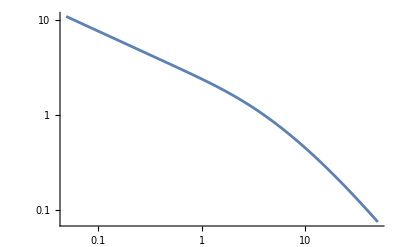

```mathematica
LogLogPlot[(3 ⅇ^(-2/x) √(2/π) (-((-16+x) (-2+x) √x)+ⅇ^(2/x) (8 √(2 π) (4-5 x) Erfc[(√2)/(√x)]+√x (x^2-60 ExpIntegralEi[-2/x]))))/x^3,{x,0,50}]
```

```mathematica
FullSimplify[ψ[3,2,x],x>0]
```

(2 ⅇ^(-2/x) √(2/π) (-((-10+x) x)+ⅇ^(2/x) (x^2-16 √(2 π) √x Erfc[(√2)/(√x)]-12 ExpIntegralEi[-2/x])))/x^(5/2)

```mathematica
Series[(2 ⅇ^(-2/x) √(2/π) (-((-10+x) x)+ⅇ^(2/x) (x^2-16 √(2 π) √x Erfc[(√2)/(√x)]-12 ExpIntegralEi[-2/x])))/x^(5/2),{x,0,1},Assumptions->x>0]
```

ⅇ^(-2/x+O[x]^2) √O[x]+((2 √(2/π))/(√x)+√O[x])

```mathematica
FullSimplify[ψ[3,1/2,x],x>0]
```

$Aborted

### α=5

```mathematica
FullSimplify[ψ[5,2,x],{x>0}]
```

1/(3 x^(7/2))2 ⅇ^(-8/x) √(2/π) (x (352+(-12+x) x)-4 ⅇ^(6/x) x (22+(-3+x) x)+ⅇ^(8/x) (3 x^3+128 √(2 π) √x (Erfc[(√2)/(√x)]-8 Erfc[(2 √2)/(√x)])+80 (-16 ExpIntegralEi[-8/x]+ExpIntegralEi[-2/x])))

General::munfl: Exp[-4095.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4103.74] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1030.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

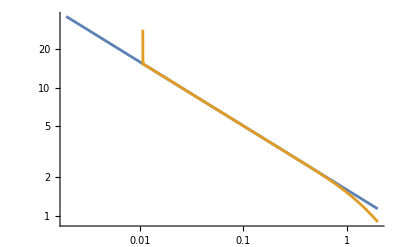

```mathematica
LogLogPlot[{2 √(2/(π x)),1/(3 x^(7/2))2 ⅇ^(-8/x) √(2/π) (x (352+(-12+x) x)-4 ⅇ^(6/x) x (22+(-3+x) x)+ⅇ^(8/x) (3 x^3+128 √(2 π) √x (Erfc[(√2)/(√x)]-8 Erfc[(2 √2)/(√x)])+80 (-16 ExpIntegralEi[-8/x]+ExpIntegralEi[-2/x])))},{x,0,2}]
```

```mathematica
FullSimplify[ψ[5,5,x],{x>0}]
```

-1/(9 x^(11/2))8 √(2/π) (-64512 HypergeometricPFQ[{1/2,1,1},{3,7/2,6},-8/x]+252 HypergeometricPFQ[{1/2,1,1},{3,7/2,6},-2/x]+5 (32512 √(2 π) √x-107136 √(2 π) x^(3/2)+7056 √(2 π) x^(5/2)-1134 x^3+1260 x^2 (-5+30 EulerGamma+94 Log[2])-315 x (-945+252 EulerGamma+764 Log[2])+3780 (21-10 x) x Log[x]))

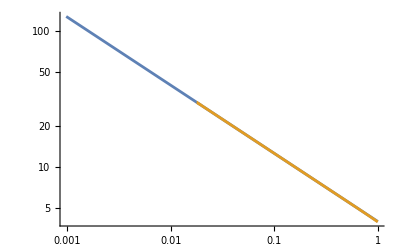

```mathematica
LogLogPlot[{(5 √2)/(√(π x)),-1/(9 x^(11/2))8 √(2/π) (-64512 HypergeometricPFQ[{1/2,1,1},{3,7/2,6},-8/x]+252 HypergeometricPFQ[{1/2,1,1},{3,7/2,6},-2/x]+5 (32512 √(2 π) √x-107136 √(2 π) x^(3/2)+7056 √(2 π) x^(5/2)-1134 x^3+1260 x^2 (-5+30 EulerGamma+94 Log[2])-315 x (-945+252 EulerGamma+764 Log[2])+3780 (21-10 x) x Log[x]))},{x,0,1}]
```

```mathematica
Series[-1/(9 x^(11/2))8 √(2/π) (-64512 HypergeometricPFQ[{1/2,1,1},{3,7/2,6},-8/x]+252 HypergeometricPFQ[{1/2,1,1},{3,7/2,6},-2/x]+5 (32512 √(2 π) √x-107136 √(2 π) x^(3/2)+7056 √(2 π) x^(5/2)-1134 x^3+1260 x^2 (-5+30 EulerGamma+94 Log[2])-315 x (-945+252 EulerGamma+764 Log[2])+3780 (21-10 x) x Log[x])),{x,0,3},Assumptions->{x>0}]
```

1/O[x]^2+(ⅇ^(-8/x+O[x]^2)+ⅇ^(-2/x+O[x]^2)) √O[x]

```mathematica
Gamma[(1+5)/2]/(√π Beta[5,5])2^(5/2)//Simplify
```

5040 √(2/π)